# Examples

## Cylinder on inclined slope

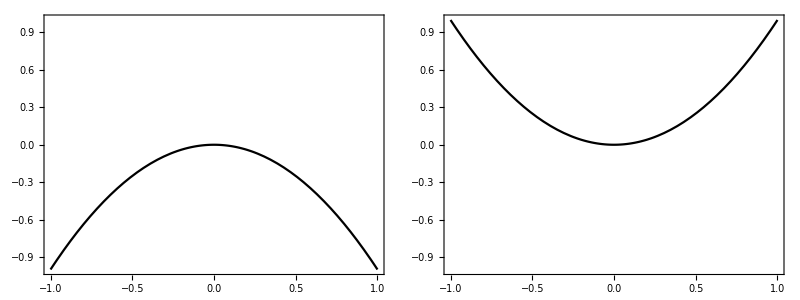

```mathematica
Grid[{{
Plot[-x^2,{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->Automatic,Frame->True,PlotStyle->Black,ImageSize->300],

Plot[x^2,{x,-1,1},PlotRange->{{-1,1},{-1,1}},AspectRatio->Automatic,Frame->True,PlotStyle->Black,ImageSize->300]}}]
```

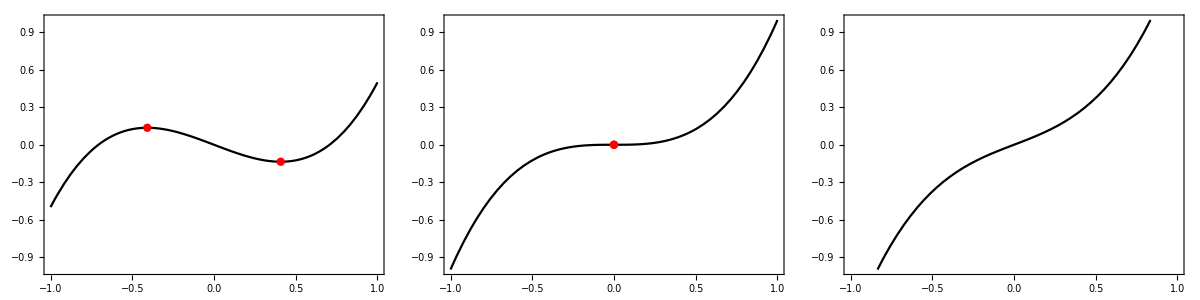

```mathematica
Grid[{Table[
Show[
Plot[x^3+u x,{x,-1,1},ImageSize->300,Frame->True,PlotStyle->Black,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}}],
ListPlot[{x,x^3+u x}/.Solve[3 x^2+u==0,x],PlotStyle->{Red,PointSize[0.02]}]
]
,{u,{-0.5,0,0.5}}]}]
```

## Zeeman catastrophe machine

```mathematica
ContourPlot3D[4 x^3-2 u x+v==0,{u,-1,1},{v,-1,1},{x,-1,1},AxesLabel->{"x","u","v"},ImageSize->300,PlotPoints->100,ViewPoint->{Top,Right}]
```

-Graphics3D-

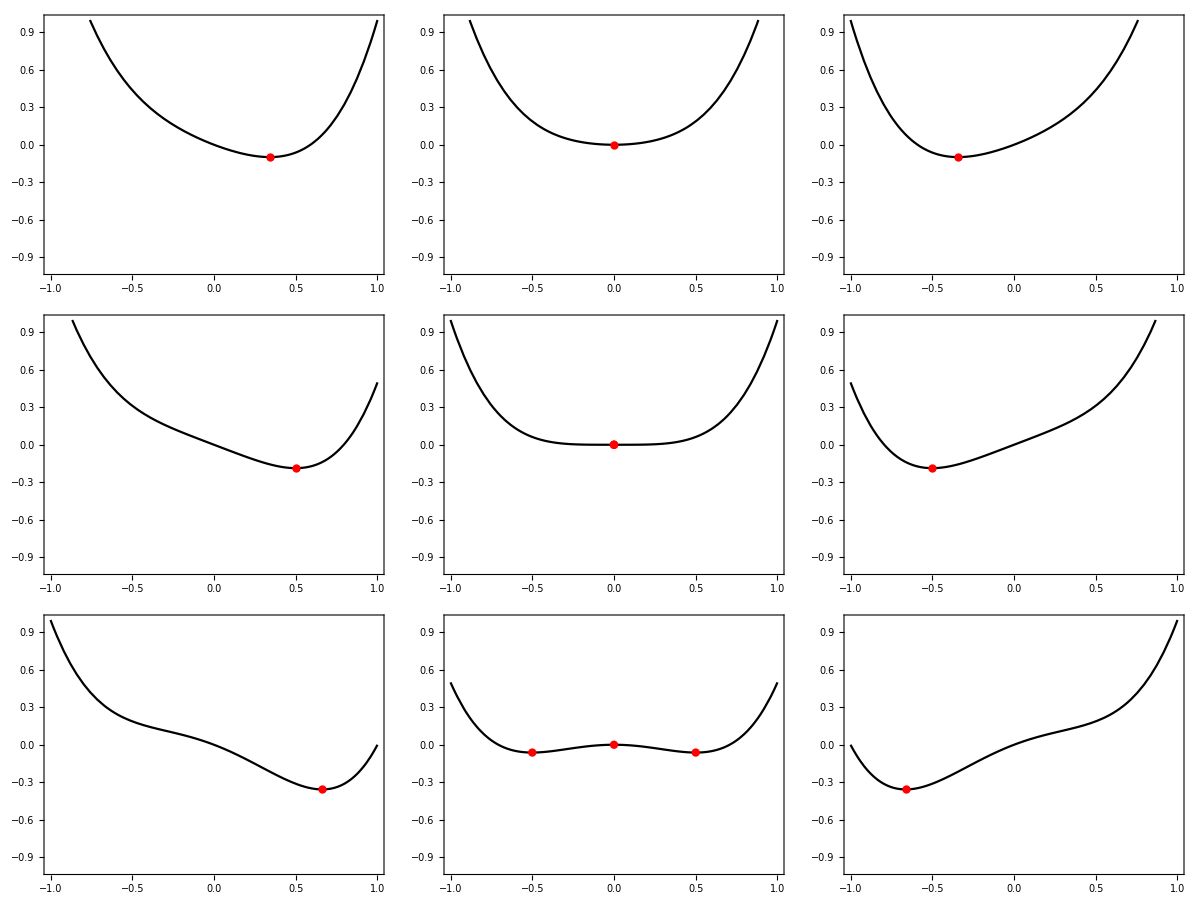

```mathematica
Grid[Table[
Show[
Plot[x^4-u x^2+v x,{x,-1,1},ImageSize->300,Frame->True,PlotStyle->Black,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}}],
ListPlot[{x,x^4-u x^2+v x}/.Solve[4 x^3-2u x+v==0,x],PlotStyle->{Red,PointSize[0.02]}]
]
,{u,{-0.5,0,0.5}},{v,{-0.5,0,0.5}}]
]
```